1. whatever the project says

```mathematica
f[x_]=x^2-2
```

-2+x^2

```mathematica
f[7]
```

47

```mathematica
g[x_]=Exp[x]
```

ⅇ^x

```mathematica
g[2]
```

ⅇ^2

```mathematica
N[%]
```

7.38906

```mathematica
h[x_]=Log[x]
```

Log[x]

```mathematica
j[x_]=Sin[3x]
```

Sin[3 x]

```mathematica
j[π/4]
```

1/(√2)

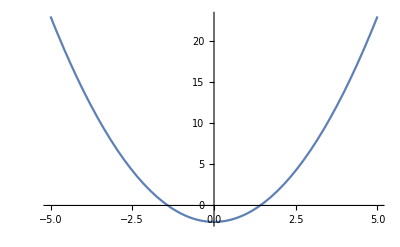

```mathematica
p1=Plot[f[x],{x,-5,5}]
```

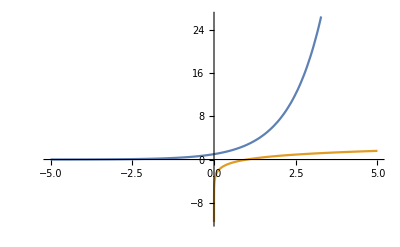

```mathematica
p2=Plot[{g[x],h[x]},{x,-5,5}]
```

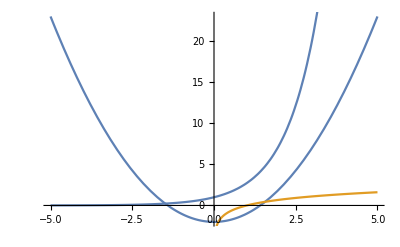

```mathematica
Show[p1,p2]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
f[x_]=(x-1)/(x^2-1)
```

(-1+x)/(-1+x^2)

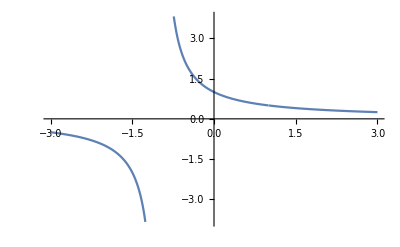

```mathematica
(-1+x)/(-1+x^2)
Plot[f[x],{x,-3,3}]
```

```mathematica
{0.5,0.9,0.99,0.999,0.9999,1,1.0001,1.001,1.01,1.1,1.5}
```

{0.5,0.9,0.99,0.999,0.9999,1,1.0001,1.001,1.01,1.1,1.5}

```mathematica
f[%]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{0.666667,0.526316,0.502513,0.50025,0.500025,Indeterminate,0.499975,0.49975,0.497512,0.47619,0.4}

```mathematica
%//TableForm
```

0.666667
0.526316
0.502513
0.50025
0.500025
Indeterminate
0.499975
0.49975
0.497512
0.47619
0.4

```mathematica
g[x_]=(x^3-27)/(x^2-9)
```

(-27+x^3)/(-9+x^2)

```mathematica
Limit[g[x],x->3]
```

```mathematica
9/2
ClearAll
```

9/2

ClearAll

```mathematica
f[x_]=x^3+2x+1
```

1+2 x+x^3

```mathematica
f'[x]
```

2+3 x^2

```mathematica
D[Cos[x],{x,27}]
```

Sin[x]

```mathematica
m=f'[1]
```

5

```mathematica
Solve[y-4==m*(x-1),y]
```

{{y→-1+5 x}}

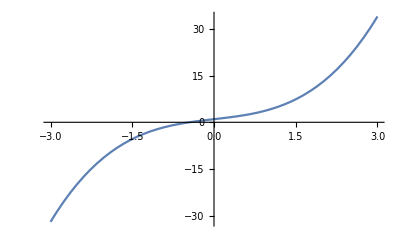

```mathematica
p1=Plot[f[x],{x,-3,3}]
```

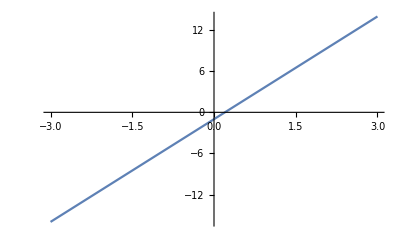

```mathematica
p2=Plot[-1+5 x,{x,-3,3}]
```

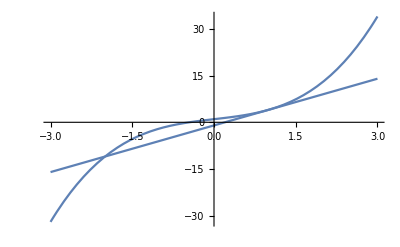

```mathematica
Show[p1,p2]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
Show[p1]
```

-Graphics-

```mathematica
Dt[x^2+2x*y+4y^2==12,x]
```

2 x+2 y+2 x Dt[y,x]+8 y Dt[y,x]==0

```mathematica
Solve[%,Dt[y,x]]
```

{{Dt[y,x]→(-x-y)/(x+4 y)}}

```mathematica
g[x_,y_]=(-x-y)/(x+4 y)
```

(-x-y)/(x+4 y)

```mathematica
m=g[2,1]
```

-1/2

```mathematica
ClearAll
```

ClearAll

```mathematica
Solve[x^2-4==0]
```

{{x→-2},{x→2}}

```mathematica
Solve[Exp[x]==3-2x,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1/2 (3-2 ProductLog[ⅇ^(3/2)/2])}}

```mathematica
Reduce[Exp[x]==3-2x,x]
```

C[1]∈ℤ&&x==3/2-ProductLog[C[1],ⅇ^(3/2)/2]

```mathematica
FindRoot[Exp[x]==3-2x,{x,0.5}]
```

{x→0.594205}

```mathematica
Reduce[{x^2-4<0},x]
```

-2<x<2